```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
dirName="/home/dan/ResearchLocal/"
SetDirectory[dirName];
```

/home/dan/ResearchLocal/

### Setup

```mathematica
βmax=Solve[{α==11*β^(-1/2),α==10^-2},β][[1,1,2]]
βmin=Solve[{α==11*β^(-1/2),α==10^0},β][[1,1,2]]
```

1210000

121

```mathematica
eqTab1={
ν==α cs h,
cs^2==(kb Tc)/(μ mp),
ρ==1/(√(2 π))Σ/h,
h==cs/Ω,
Tc^4==3/4 τ Tdisk^4,
τ==1/2 Σ κR,
ν Σ==mdot/(3π),
σ Tdisk^4==9/8 ν Σ Ω^2,
κR==κR0
};
eqTab2={
ν==α cs h,
cs^2==(kb Tc)/(μ mp),
ρ==1/(√(2 π))Σ/h,
h==cs/Ω,
Tc^4==3/4 τ Tdisk^4,
τ==1/2 Σ κR,
ν Σ==mdot/(3π),
σ Tdisk^4==9/8 ν Σ Ω^2,
κR==κR0*ρ,
β== (ρ cs^2)/Bz^2,
α== 11*β^(-1/2)
};
rulesTab={ν>0,α>0,cs>0,h>0,kb>0,Tc>0,μ>0,mp>0,ρ>0,Σ>0,Ω>0,τ>0,Tdisk>0,τ>0,mdot>0,σ>0,κR>0,κR0>0,Tc>0,β>0,Bz>0,b1>0,b2>0};
```

### Known mdot, solving for Σ, constant alpha

```mathematica
sol1=Solve[Flatten[{eqTab1,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ},Reals];
red1=Reduce[Flatten[{eqTab1,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ},Reals];
Table[ToRadicals[red1[[i]]],{i,13,Length[red1]}]//TableForm
```

Tc==((-1)^(2/5) (3/2)^(1/5) mdot^(2/5) mp^(1/5) κR0^(1/5) μ^(1/5) Ω^(3/5))/(2 kb^(1/5) π^(2/5) α^(1/5) σ^(1/5))
Tdisk==-(mdot^(1/4) (3/π)^(1/4) √Ω)/(2^(3/4) σ^(1/4))
cs==(√((Tdisk^8 κR0 σ)/(Tc^4 α Ω)))/(√3)
ρ==(4 √(2/π) Tdisk^4 σ)/(9 cs^3 α)
h==cs/Ω
κR==(3 cs h Tc^4 α Ω^2)/(Tdisk^8 σ)
ν==cs h α
τ==(4 Tc^4)/(3 Tdisk^4)
Σ==(8 Tdisk^4 σ)/(9 ν Ω^2)

### Known mdot, solving for Σ, variable alpha

```mathematica
sol2=Solve[Flatten[{eqTab2,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ,β,α},Reals];
red2=Reduce[Flatten[{eqTab2,rulesTab}],{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ,β,α},Reals];
Table[ToRadicals[red2[[i]]],{i,11,Length[red2]}]//TableForm
```

Tc==((-1)^(2/15) mdot^(2/3) mp^(7/15) κR0^(2/15) μ^(7/15) Ω^(6/5))/(2 3^(4/15) 11^(8/15) Bz^(8/15) kb^(7/15) π^(13/15) σ^(2/15))
Tdisk==-(mdot^(1/4) (3/π)^(1/4) √Ω)/(2^(3/4) σ^(1/4))
cs==√((kb Tc)/(mp μ))
ρ==(32 Tdisk^8 σ^2)/(9801 Bz^2 cs^4 π)
h==cs/Ω
κR==κR0 ρ
ν==(11 cs h)/(√((cs^2 ρ)/Bz^2))
τ==(4 Tc^4)/(3 Tdisk^4)
Σ==(8 Tdisk^4 σ)/(9 ν Ω^2)
β==(cs^2 ρ)/Bz^2
α==ν/(cs h)

### Plot for constant alpha

```mathematica
kb=1;mp=1;μ=1;σ=1;
κR0=0.01;
G=1;M=1;
mdot=0.0001;
```

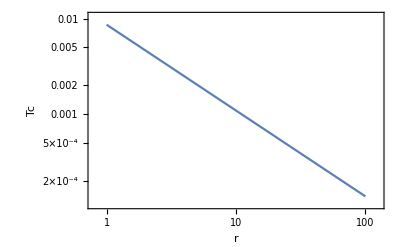
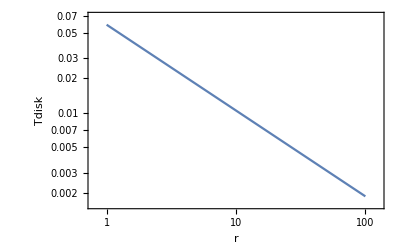
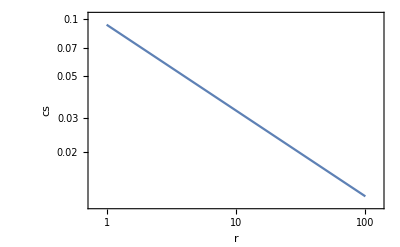
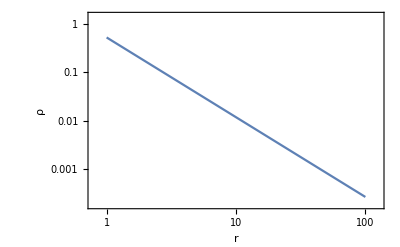
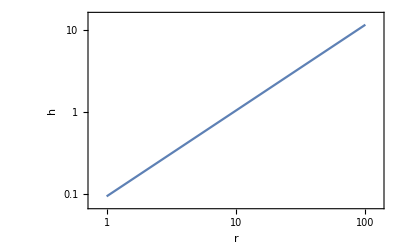
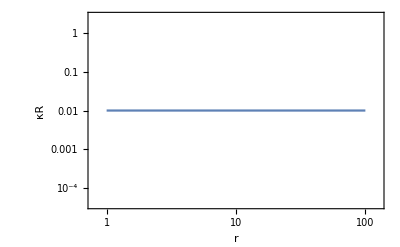
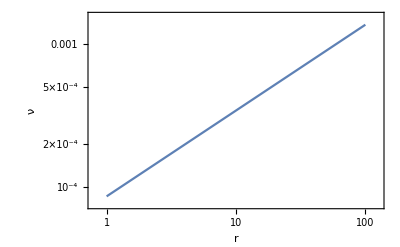
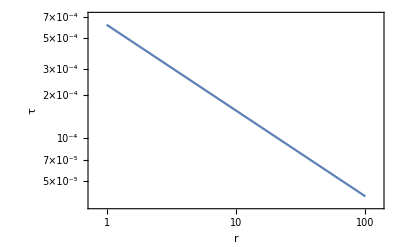

```mathematica
Table[
LogLogPlot[sol1[[1,i,2,1]]/.{Ω->√((G*M)/r^3),α->0.01},{r,1,100},
Frame->True,
FrameLabel->{"r",sol1[[1,i,1]]}]
,{i,1,9}]
```

### Plot for variable alpha

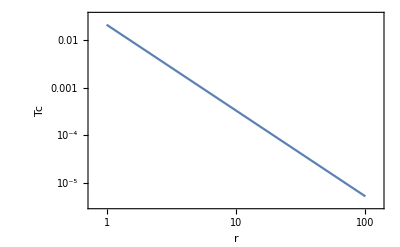
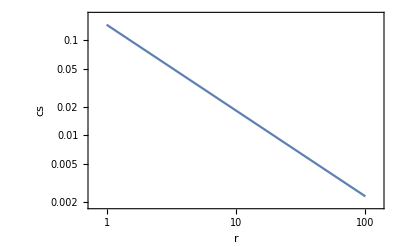
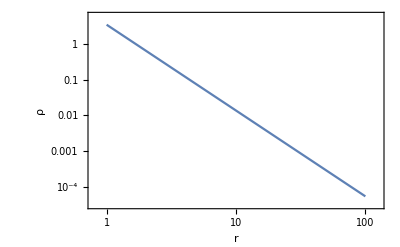
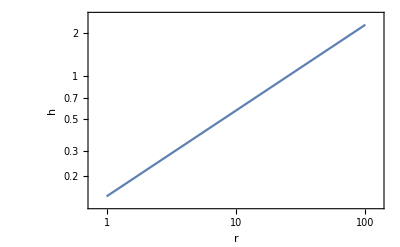
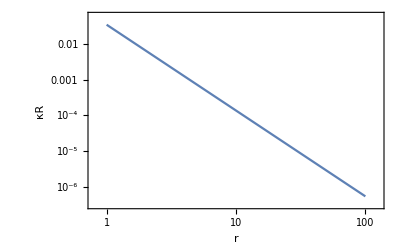
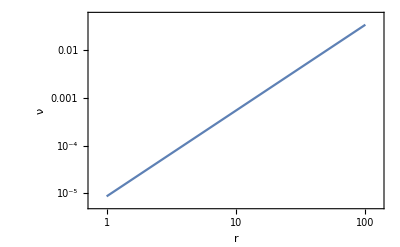
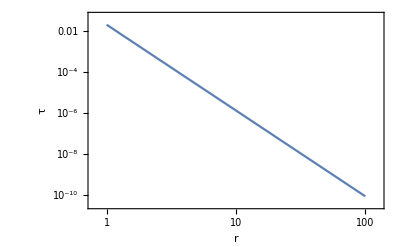
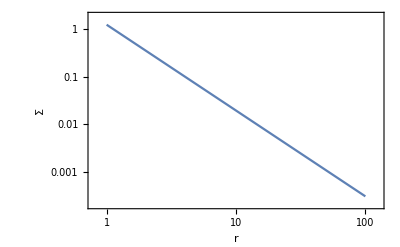
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
LogLogPlot[sol2[[1,i,2,1]]/.{Ω->√((G*M)/r^3),Bz->10^-5},{r,1,100},
Frame->True,
FrameLabel->{"r",sol2[[1,i,1]]}]
,{i,1,11}]
```

### Patch together the 2 solutions

```mathematica
Table[sol2[[1,i,1]],{i,1,11}]
```

{Tc,Tdisk,cs,ρ,h,κR,ν,τ,Σ,β,α}

```mathematica
getConstAlphaSol[r_,α1_]:=Evaluate[Table[sol1[[1,i,2,1]]/.{Ω->√((G*M)/r^3),α->α1},{i,1,9}]]
getVarAlphaSol[r_,Bz1_]:=Evaluate[Table[sol2[[1,i,2,1]]/.{Ω->√((G*M)/r^3),Bz->Bz1},{i,1,11}]]
```

```mathematica
getSol[r0_,Bz10_]:=Module[{r=r0,Bz1=Bz10,αSol,α1,solTemp,solFinal},
αSol=getVarAlphaSol[r,Bz1][[11]];
If[αSol>1.0,α1=1.0];
If[αSol<0.01,α1=0.01];
If[1.0>αSol>0.01,α1=αSol];
solTemp=getConstAlphaSol[r,α1];
solFinal=Flatten[{solTemp,solTemp[[4]] solTemp[[3]]^2/Bz1^2,α1}];
solFinal
]
```

```mathematica
rTab=Table[10^i,{i,0,2,0.05}];
getSolTab[Bz_]:=Table[getSol[r,Bz],{r,rTab}];
plotSol[Bz_,col_]:=ListLogLogPlot[Transpose[{rTab,getSolTab[Bz][[All,col]]}],
Frame->True,Joined->True,ImageSize->Medium,
FrameLabel->{"r",sol2[[1,col,1]]}]
```

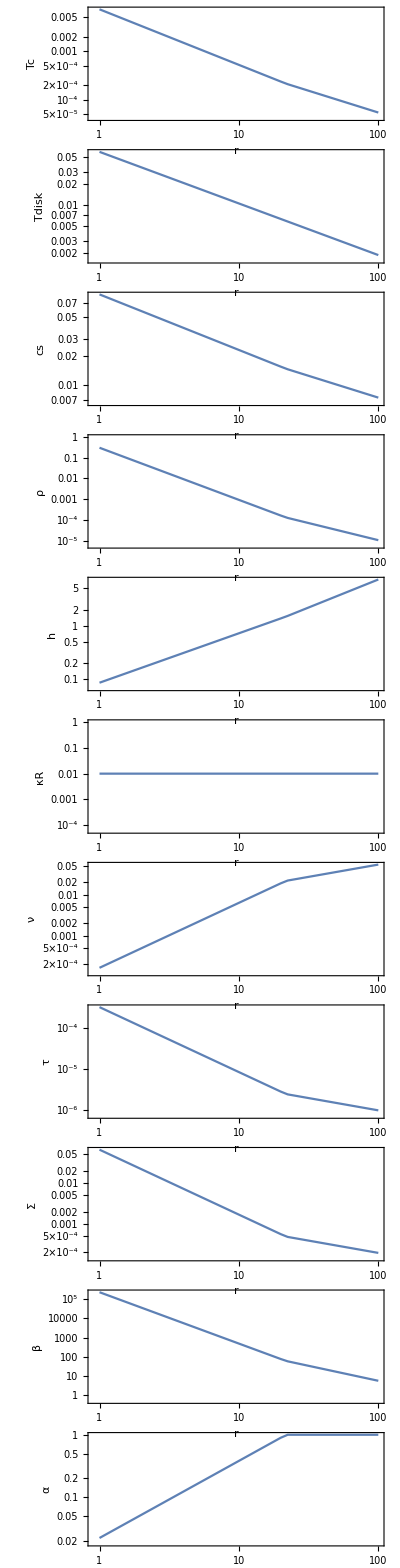

```mathematica
Table[plotSol[10^-4*r^(-1/2),col],{col,1,11}]//TableForm
```

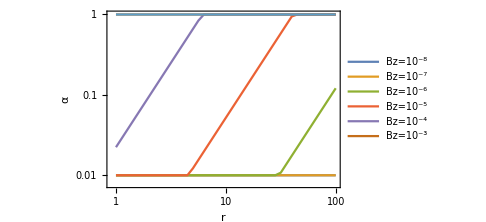

```mathematica
col=11;
ListLogLogPlot[Table[Transpose[{rTab,getSolTab[10^i][[All,col]]}],{i,-8,-2}],
Frame->True,Joined->True,ImageSize->Medium,
FrameLabel->{"r",sol2[[1,col,1]]},
PlotLegends->{"Bz=10^-8","Bz=10^-7","Bz=10^-6","Bz=10^-5","Bz=10^-4","Bz=10^-3"}]
```